# Overlap Integrals for Non-adiabatic PCET rate expressions

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/souda/Documents/Mathematica notebooks

## Constants

### Unit conversions

```mathematica
bohr2a=0.529177;
a2bohr=1/bohr2a;
au2kcal=627.5095;
kcal2au=1/au2kcal;
ev2cm=8065.54477;
cm2ev = 1/ev2cm ;
au2ev=27.2113 ;
ev2au = 1/au2ev;
cm2au=cm2ev*ev2au;     
au2cm=1/cm2au;
au2ps=2.4189 10^-5;
```

### Universal constants

```mathematica
ℏ=1;
hbarps=0.047685388/(au2kcal π);
Dalton=1822.8880;
μH=1836.1526675;
μD=3670.4829550;
kb=3.16683 10^-6;
```

### Accuracy settings

```mathematica
AccN=50;
```

## Morse potentials for D-H (reactant) and A-H (product) bonds

### Proton transfer interface geometry

```mathematica
RCH=0.98;
ROH=0.97;
```

Distance between minima of reactant and product potential energy curves (R0) in Bohrs.

```mathematica
R0[RDA_]:=(RDA-RCH-ROH)a2bohr;
RDA[R_]:=R bohr2a+RCH+ROH;
```

### Morse parameters (1 - reactant; 2 - product)

β parameter (Å^-1) from frequency ω (cm^-1), mass μ (amu), and dissociation energy D (kcal/mol).

```mathematica
βMorse[ω_,D_,μ_]:=(ω cm2au √((μ Dalton)/(2D kcal2au)))1/bohr2a;
```

```mathematica
D1=49.7 kcal2au;
β1=3.32/a2bohr;
Print["Reactant proton vibrational frequency: ",Panel[au2cm β1 √((2D1)/μH)]," cm^-1"];
Print["Reactant deuteron vibrational frequency: ",Panel[au2cm β1 √((2D1)/μD)]," cm^-1"];
```

Reactant proton vibrational frequency: 3581.38 cm^-1

Reactant deuteron vibrational frequency: 2533.05 cm^-1

```mathematica
D2=68.96 kcal2au;
β2=2.828/a2bohr;
Print["Product proton vibrational frequency: ",Panel[au2cm β2 √((2D2)/μH)]," cm^-1"];
Print["Product deuteron vibrational frequency: ",Panel[au2cm β2 √((2D2)/μD)]," cm^-1"];
```

Product proton vibrational frequency: 3593.46 cm^-1

Product deuteron vibrational frequency: 2541.59 cm^-1

Morse potentials (equlibrium position at x=0):

```mathematica
U1[x_]:=D1(1-Exp[-β1 x])^2;
U2[x_]:=D2(1-Exp[-β2 x])^2;
```

```mathematica
au2cm √(2.963/a2bohr^2 1/μH)
```

4665.47

```mathematica
βMorse[3586,49.7,μH/Dalton]
```

3.32428

## Harmonic potentials for D-H (reactant) and A-H (product) bonds

Frequencies:

```mathematica
ω1H=β1 √((2D1)/μH);
ω2H=β2 √((2D2)/μH);
ω1D=β1 √((2D1)/μD);
ω2D=β2 √((2D2)/μD);
```

Harmonic potentials (equlibrium position at x=0):

```mathematica
Uharm1[x_]:=β1^2 D1 x^2;
Uharm2[x_]:=β2^2 D2 x^2;
```

## Analytical expressions for harmonic oscillator energies and wavefunctions

Energies:

```mathematica
ϵharm[n_,ω_]:=SetAccuracy[ℏ ω cm2au(n+1/2),AccN];
```

Wavefunctions:

```mathematica
ψharm[x_,x0_,M_,ω_,n_]:=SetAccuracy[((M Dalton ω cm2au)/(π ℏ))^(1/4)1/(2^(n/2)√(n!))Exp[-(M Dalton ω cm2au)/(2ℏ) (x-x0)^2]HermiteH[n,(x-x0)√((M Dalton ω cm2au)/ℏ)],AccN];
```

## Analytical expressions for the Morse wavefunctions from [J. P. Dahl, M. Springborg, J. Chem. Phys. 88, 4535 (1987)] (typo in Eq.(38): factor √α is missing)

```mathematica
λ1=SetAccuracy[(√(2μH D1))/(β1 ℏ),AccN];
```

```mathematica
λ1D=SetAccuracy[(√(2μD D1))/(β1 ℏ),AccN];
```

```mathematica
λ2=SetAccuracy[(√(2μH D2))/(β2 ℏ),AccN];
```

```mathematica
λ2D=SetAccuracy[(√(2μD D2))/(β2 ℏ),AccN];
```

```mathematica
ξ1[x_]:=SetAccuracy[2λ1 Exp[-β1 x],AccN];
```

```mathematica
ξ1D[x_]:=SetAccuracy[2λ1D Exp[-β1 x],AccN];
```

```mathematica
ξ2[x_]:=SetAccuracy[2λ2 Exp[-β2 x],AccN];
```

```mathematica
ξ2D[x_]:=SetAccuracy[2λ2D Exp[-β2 x],AccN];
```

```mathematica
E1[n_]:=SetAccuracy[((n+1/2)-1/(2λ1)(n+1/2)^2)ℏ √((2D1 β1^2)/μH),AccN];
```

```mathematica
E1D[n_]:=SetAccuracy[((n+1/2)-1/(2λ1D)(n+1/2)^2)ℏ √((2D1 β1^2)/μD),AccN];
```

```mathematica
E2[n_]:=SetAccuracy[((n+1/2)-1/(2λ2)(n+1/2)^2)ℏ √((2D2 β2^2)/μH),AccN];
```

```mathematica
E2D[n_]:=SetAccuracy[((n+1/2)-1/(2λ2D)(n+1/2)^2)ℏ √((2D2 β2^2)/μD),AccN];
```

```mathematica
N1D[n_]:=SetAccuracy[√((β1(2λ1D-2n-1)Gamma[n+1])/Gamma[2λ1D-n]),AccN];
```

```mathematica
N2D[n_]:=SetAccuracy[√((β2(2λ2D-2n-1)Gamma[n+1])/Gamma[2λ2D-n]),AccN];
```

```mathematica
N1[n_]:=SetAccuracy[√((β1(2λ1-2n-1)Gamma[n+1])/Gamma[2λ1-n]),AccN];
```

```mathematica
N2[n_]:=SetAccuracy[√((β2(2λ2-2n-1)Gamma[n+1])/Gamma[2λ2-n]),AccN];
```

```mathematica
ϕ1[x_,n_]:=SetAccuracy[N1[n]Exp[-ξ1[x]/2] ξ1[x]^(λ1-n-1/2)LaguerreL[n,2λ1-2n-1,ξ1[x]],AccN];
```

```mathematica
ϕ1D[x_,n_]:=SetAccuracy[N1D[n]Exp[-ξ1D[x]/2] ξ1D[x]^(λ1D-n-1/2)LaguerreL[n,2λ1D-2n-1,ξ1D[x]],AccN];
```

```mathematica
ϕ2[x_,n_]:=SetAccuracy[N2[n]Exp[-ξ2[x]/2] ξ2[x]^(λ2-n-1/2)LaguerreL[n,2λ2-2n-1,ξ2[x]],AccN];
```

```mathematica
ϕ2D[x_,n_]:=SetAccuracy[N2D[n]Exp[-ξ2D[x]/2] ξ2D[x]^(λ2D-n-1/2)LaguerreL[n,2λ2D-2n-1,ξ2D[x]],AccN];
```

Number of bound states:

```mathematica
Nbound1=IntegerPart[λ1-1/2];
Nbound2=IntegerPart[λ2-1/2];
Nbound1D=IntegerPart[λ1D-1/2];
Nbound2D=IntegerPart[λ2D-1/2];
```

```mathematica
NboundMin=Min[Nbound1,Nbound2,Nbound1D,Nbound2D]
```

9

## Harmonic overlap integrals [J.-L. Chang, J. Mol. Spectrosc. 232 (2005) 102-104]

```mathematica
σH[R_,n_,m_]:=Module[{K,α1,α2,s,A,Prefactor,b1,b2,i,j},
α1=(μH ω1H)/ℏ;
α2=(μH ω2H)/ℏ;
s=(α1 α2 R^2)/(α1+α2);
A=(2 √(α1 α2))/(α1+α2);
K[i_,j_]:=If[OddQ[i+j],0,((i+j-1)!!)/(α1+α2)^((i+j)/2)];
Prefactor=√((A Exp[-s])/(2^(n+m)n!m!));
b1=-(R α2 √α1)/(α1+α2);
b2=(R α1 √α2)/(α1+α2);
Prefactor∑_(i=0)^n (∑_(j=0)^m (Binomial[n,i]Binomial[m,j]HermiteH[n-i,b1]HermiteH[m-j,b2](2 √α1)^i(2 √α2)^j K[i,j]))

];
```

```mathematica
σD[R_,n_,m_]:=Module[{K,α1,α2,s,A,Prefactor,b1,b2,i,j},
α1=(μD ω1D)/ℏ;
α2=(μD ω2D)/ℏ;
s=(α1 α2 R^2)/(α1+α2);
A=(2 √(α1 α2))/(α1+α2);
K[i_,j_]:=If[OddQ[i+j],0,((i+j-1)!!)/(α1+α2)^((i+j)/2)];
Prefactor=√((A Exp[-s])/(2^(n+m)n!m!));
b1=-(R α2 √α1)/(α1+α2);
b2=(R α1 √α2)/(α1+α2);
Prefactor∑_(i=0)^n (∑_(j=0)^m (Binomial[n,i]Binomial[m,j]HermiteH[n-i,b1]HermiteH[m-j,b2](2 √α1)^i(2 √α2)^j K[i,j]))

];
```

```mathematica
αharmH[R_,i_,j_]:=Module[{x},
-1/σH[R,i,j]*D[σH[x,i,j],x]/.x->R];
αharmD[R_,i_,j_]:=Module[{x},
-1/σD[R,i,j]*D[σD[x,i,j],x]/.x->R];
```

```mathematica
γharmH[R_,i_,j_]:=Module[{x,D1,D2},
D1=D[σH[x,i,j],x]/.x->R;
D2=D[σH[x,i,j],{x,2}]/.x->R;
-1/σH[R,i,j]*D2+1/σH[R,i,j]^2 D1^2
];
γharmD[R_,i_,j_]:=Module[{x,D1,D2},
D1=D[σD[x,i,j],x]/.x->R;
D2=D[σD[x,i,j],{x,2}]/.x->R;
-1/σD[R,i,j]*D2+1/σD[R,i,j]^2 D1^2
];
```

```mathematica
αharmH[R0[2.7],0,0]
```

21.2685

```mathematica
γharmH[R0[2.7],0,0]
```

15.0064

```mathematica
λaharmH=Function[{R,μ,i,j},SetAccuracy[(ℏ^2 αharmH[R,i,j]^2)/(2μ Dalton),AccN]];
λaharmD=Function[{R,μ,i,j},SetAccuracy[(ℏ^2 αharmD[R,i,j]^2)/(2μ Dalton),AccN]];
λgharmH=Function[{R,μ,i,j},SetAccuracy[(ℏ^2 γharmH[R,i,j])/(2μ Dalton),AccN]];
λgharmD=Function[{R,μ,i,j},SetAccuracy[(ℏ^2 γharmD[R,i,j])/(2μ Dalton),AccN]];
```

Quality of expansions for harmonic overlaps:

```mathematica
σHexp1[R_,Req_,i_,j_]:=σH[R0[Req],i,j]Exp[-αharmH[R0[Req],i,j](R0[R]-R0[Req])];
σHexp2[R_,Req_,i_,j_]:=σH[R0[Req],i,j]Exp[-αharmH[R0[Req],i,j](R0[R]-R0[Req])-1/2 γharmH[R0[Req],i,j](R0[R]-R0[Req])^2];
```

```mathematica
σDexp1[R_,Req_,i_,j_]:=σD[R0[Req],i,j]Exp[-αharmD[R0[Req],i,j](R0[R]-R0[Req])];
σDexp2[R_,Req_,i_,j_]:=σD[R0[Req],i,j]Exp[-αharmD[R0[Req],i,j](R0[R]-R0[Req])-1/2 γharmD[R0[Req],i,j](R0[R]-R0[Req])^2];
```

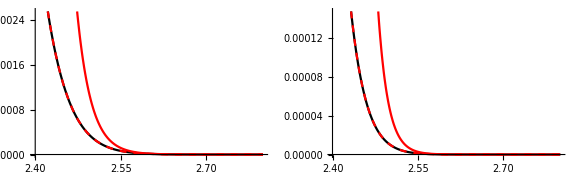

```mathematica
RR=2.7;
GraphicsRow[
{
Plot[{σH[R0[R],0,0],σHexp1[R,RR,0,0],σHexp2[R,RR,0,0]},{R,2.4,2.8},PlotStyle->{Black,Red,{Red,Dashed}}],
Plot[{σD[R0[R],0,0],σDexp1[R,RR,0,0],σDexp2[R,RR,0,0]},{R,2.4,2.8},PlotStyle->{Black,Red,{Red,Dashed}}]
},
ImageSize->Large]
```

## Morse overlap integrals in terms of the Wigner function based on [J. C. Lopez, A. L. Rivera, Yu. F. Smirnov, A. Frank, arXiv:physics/0109017v]

General case:

```mathematica
FCH[R_,nu1_,nu2_]:=
Module[{AccN,Acc,l1,l2,j1, beta1, j2, beta2,y1,y2,a,Fcsum,fac0a,fac0b,fac0,fac1a,fac1b,fac1,fac2,fac3,Fcaux,Lambda,aux,peak,xatmax,fatmax,integr,res,finteg2,smallestx,x,X},
(*-----------------------------------------------------------------------*)(* This program computes the Franck-Condon factor of two Morse functions *)
(* for the mirrored potentials *)
(* Modified version of Lopez-Rivera-Smirnov-Frank *)
(* Usage: *)
(* FCH[R,nu1,nu2] *)
(*---------------------------------------------------------------------*)(* Accuracies: *)
Acc=15;
AccN=60;
j1=SetAccuracy[λ1-1/2,AccN];
j2=SetAccuracy[λ2-1/2,AccN];
beta1=SetAccuracy[β1,AccN];
beta2=SetAccuracy[β2,AccN];
a=SetAccuracy[beta2/beta1,AccN];
y1=SetAccuracy[(2*j1+1)*Exp[-beta1*R/2],AccN];
y2=SetAccuracy[(2*j2+1)*Exp[-beta2*R/2],AccN];
Fcsum=0;
fac0a=SetAccuracy[2*Sqrt[a*FullSimplify[nu1!*(j1-nu1)*nu2!*(j2-nu2)/(Gamma[2*j1-nu1+1]*Gamma[2*j2-nu2+1])]],AccN];
fac0b=SetAccuracy[y1^(j1-nu1)*y2^(j2-nu2),AccN];
fac0=fac0a*fac0b;
Do[(*Do loops for summations*)
fac1a=SetAccuracy[(2*j1+1)^(l1)*(2*j2+1)^(l2),AccN];
fac1b=SetAccuracy[Exp[-beta1*R*(l1)/2]*Exp[-beta2*R*(l2)/2],AccN];
fac1=SetAccuracy[fac1a*fac1b,AccN];
fac2=SetAccuracy[(-1)^(l1+l2)/(l1!*l2!),AccN];
fac3=SetAccuracy[FullSimplify[Binomial[2*j1-nu1,nu1-l1]*Binomial[2*j2-nu2,nu2-l2]],AccN];
Fcaux=SetAccuracy[fac0*fac1*fac2*fac3,AccN];
(* ===========================================================*)
(* Integration Section *)
(* Integral Ia.Calculation with scaling *)
(* ===========================================================*)Lambda=SetAccuracy[j1-nu1+l1-a*(j2-nu2+l2),AccN];
(* Integrand *)
integr=SetAccuracy[x^(Lambda-1)*Exp[-(y1*x+y2*x^(-a))/2],AccN];
finteg[xx_]:=xx^(Lambda-1)*Exp[-(y1*xx+y2*xx^(-a))/2];
(* Find smallest x before underflow occurs *)
Off[General::"unfl"];
smallestx=0.1`100;
While[finteg[smallestx]>$MinNumber,smallestx=smallestx/2];
smallestx=smallestx*2;
On[General::unfl];
(*Looking for position of maximum*)
aux=FindMaximum[integr,{x,smallestx+1,smallestx,∞},WorkingPrecision->AccN];
peak=aux[[2]][[1]][[2]];
xatmax=SetAccuracy[peak,AccN];
(*Integrand value at maximum*)
fatmax=SetAccuracy[finteg[peak],AccN];
finteg2=SetAccuracy[(1/fatmax)*(X*xatmax)^(Lambda-1)*Exp[-(y1*(X*xatmax)+y2*(X*xatmax)^(-a))/2],AccN];
res=SetAccuracy[fatmax*xatmax*NIntegrate[finteg2,{X,0,Infinity},PrecisionGoal->Acc,AccuracyGoal->Acc,Method->"DoubleExponential"],AccN];
(*Adding terms*)
Fcsum=Fcsum+SetAccuracy[Fcaux*res,AccN],
{l1,0,nu1},{l2,0,nu2}];
(*Output*)
Re@Fcsum
];
```

```mathematica
FCD[R_,nu1_,nu2_]:=
Module[{AccN,Acc,l1,l2,j1, beta1, j2, beta2,y1,y2,a,Fcsum,fac0a,fac0b,fac0,fac1a,fac1b,fac1,fac2,fac3,Fcaux,Lambda,aux,peak,xatmax,fatmax,integr,res,finteg2,smallestx,x,X},
(*-----------------------------------------------------------------------*)(* This program computes the Franck-Condon factor of two Morse functions *)
(* for the mirrored potentials *)
(* Modified version of Lopez-Rivera-Smirnov-Frank *)
(* Usage: *)
(* FCH[R,nu1,nu2] *)
(*---------------------------------------------------------------------*)(* Accuracies: *)
Acc=15;
AccN=60;
j1=SetAccuracy[λ1D-1/2,AccN];
j2=SetAccuracy[λ2D-1/2,AccN];
beta1=SetAccuracy[β1,AccN];
beta2=SetAccuracy[β2,AccN];
a=SetAccuracy[beta2/beta1,AccN];
y1=SetAccuracy[(2*j1+1)*Exp[-beta1*R/2],AccN];
y2=SetAccuracy[(2*j2+1)*Exp[-beta2*R/2],AccN];
Fcsum=0;
fac0a=SetAccuracy[2*Sqrt[a*FullSimplify[nu1!*(j1-nu1)*nu2!*(j2-nu2)/(Gamma[2*j1-nu1+1]*Gamma[2*j2-nu2+1])]],AccN];
fac0b=SetAccuracy[y1^(j1-nu1)*y2^(j2-nu2),AccN];
fac0=fac0a*fac0b;
Do[(*Do loops for summations*)
fac1a=SetAccuracy[(2*j1+1)^(l1)*(2*j2+1)^(l2),AccN];
fac1b=SetAccuracy[Exp[-beta1*R*(l1)/2]*Exp[-beta2*R*(l2)/2],AccN];
fac1=SetAccuracy[fac1a*fac1b,AccN];
fac2=SetAccuracy[(-1)^(l1+l2)/(l1!*l2!),AccN];
fac3=SetAccuracy[FullSimplify[Binomial[2*j1-nu1,nu1-l1]*Binomial[2*j2-nu2,nu2-l2]],AccN];
Fcaux=SetAccuracy[fac0*fac1*fac2*fac3,AccN];
(* ===========================================================*)
(* Integration Section *)
(* Integral Ia.Calculation with scaling *)
(* ===========================================================*)Lambda=SetAccuracy[j1-nu1+l1-a*(j2-nu2+l2),AccN];
(* Integrand *)
integr=SetAccuracy[x^(Lambda-1)*Exp[-(y1*x+y2*x^(-a))/2],AccN];
finteg[xx_]:=xx^(Lambda-1)*Exp[-(y1*xx+y2*xx^(-a))/2];
(* Find smallest x before underflow occurs *)
Off[General::"unfl"];
smallestx=0.1`50;
While[finteg[smallestx]>$MinNumber,smallestx=smallestx/2];
smallestx=smallestx*2;
On[General::unfl];
(*Looking for position of maximum*)
aux=FindMaximum[integr,{x,smallestx+1,smallestx,∞},WorkingPrecision->AccN];
peak=aux[[2]][[1]][[2]];
xatmax=SetAccuracy[peak,AccN];
(*Integrand value at maximum*)
fatmax=SetAccuracy[finteg[peak],AccN];
finteg2=SetAccuracy[(1/fatmax)*(X*xatmax)^(Lambda-1)*Exp[-(y1*(X*xatmax)+y2*(X*xatmax)^(-a))/2],AccN];
res=SetAccuracy[fatmax*xatmax*NIntegrate[finteg2,{X,0,Infinity},PrecisionGoal->Acc,AccuracyGoal->Acc,Method->"DoubleExponential"],AccN];
(*Adding terms*)
Fcsum=Fcsum+SetAccuracy[Fcaux*res,AccN],{l1,0,nu1},{l2,0,nu2}];
(*Output*)
Re@Fcsum
];
```

Case β_1=β_2:

```mathematica
FC0H[R_,nu1_,nu2_]:=
Module[{l1,l2,j1, beta, j2, y1,y2,Fcsum,fac0a,fac0b,fac0,fac1a,fac1b,fac1,fac2,fac3,Fcaux,Lambda,aux,res},
(*-----------------------------------------------------------------------*)(* This program computes the Franck-Condon factor of two Morse functions *)
(* for the mirrored potentials for the case when Subscript[β, 1]=Subscript[β, 2]=β *)
(* Modified version of Lopez-Rivera-Smirnov-Frank *)
(* Usage: *)
(* FC0H[R,nu1,nu2] *)
(*---------------------------------------------------------------------*)
(* Abort if Subscript[β, 1]≠Subscript[β, 2] *)
If[β1≠β2,(Print["β1≠β2: Use FCH instead..."];Abort[])];
(* Accuracies: *)
j1=SetAccuracy[λ1-1/2,AccN];
j2=SetAccuracy[λ2-1/2,AccN];
beta=SetAccuracy[β1,AccN];
y1=SetAccuracy[(2*j1+1)*Exp[-beta*R/2],AccN];
y2=SetAccuracy[(2*j2+1)*Exp[-beta*R/2],AccN];
Fcsum=0;
fac0a=SetAccuracy[2*Sqrt[FullSimplify[nu1!*(j1-nu1)*nu2!*(j2-nu2)/(Gamma[2*j1-nu1+1]*Gamma[2*j2-nu2+1])]],AccN];
fac0b=SetAccuracy[y1^(j1-nu1)*y2^(j2-nu2),AccN];
fac0=fac0a*fac0b;
Do[(*Do loops for summations*)
fac1a=SetAccuracy[(2*j1+1)^(l1)*(2*j2+1)^(l2),AccN];
fac1b=SetAccuracy[Exp[-beta*R*(l1)/2]*Exp[-beta*R*(l2)/2],AccN];
fac1=SetAccuracy[fac1a*fac1b,AccN];
fac2=SetAccuracy[(-1)^(l1+l2)/(l1!*l2!),AccN];
fac3=SetAccuracy[FullSimplify[Binomial[2*j1-nu1,nu1-l1]*Binomial[2*j2-nu2,nu2-l2]],AccN];
Fcaux=SetAccuracy[fac0*fac1*fac2*fac3,AccN];
Lambda=SetAccuracy[j1-nu1+l1-(j2-nu2+l2),AccN];
res=SetAccuracy[2(y2/y1)^(Lambda/2)BesselK[-Lambda,√(y1*y2)],AccN];
Fcsum=Fcsum+SetAccuracy[Fcaux*res,AccN],{l1,0,nu1},{l2,0,nu2}];
Fcsum];
```

```mathematica
FC0D[R_,nu1_,nu2_]:=
Module[{l1,l2,j1, beta, j2, y1,y2,Fcsum,fac0a,fac0b,fac0,fac1a,fac1b,fac1,fac2,fac3,Fcaux,Lambda,aux,res},
(*-----------------------------------------------------------------------*)(* This program computes the Franck-Condon factor of two Morse functions *)
(* for the mirrored potentials for the case when Subscript[β, 1]=Subscript[β, 2]=β *)
(* Modified version of Lopez-Rivera-Smirnov-Frank *)
(* Usage: *)
(* FC0H[R,nu1,nu2] *)
(*---------------------------------------------------------------------*)(* Abort if Subscript[β, 1]≠Subscript[β, 2] *)
If[β1≠β2,(Print["β1≠β2: Use FCD instead..."];Abort[])];
(* Accuracies: *)
j1=SetAccuracy[λ1D-1/2,AccN];
j2=SetAccuracy[λ2D-1/2,AccN];
beta=SetAccuracy[β1,AccN];
y1=SetAccuracy[(2*j1+1)*Exp[-beta*R/2],AccN];
y2=SetAccuracy[(2*j2+1)*Exp[-beta*R/2],AccN];
Fcsum=0;
fac0a=SetAccuracy[2*Sqrt[FullSimplify[nu1!*(j1-nu1)*nu2!*(j2-nu2)/(Gamma[2*j1-nu1+1]*Gamma[2*j2-nu2+1])]],AccN];
fac0b=SetAccuracy[y1^(j1-nu1)*y2^(j2-nu2),AccN];
fac0=fac0a*fac0b;
Do[(*Do loops for summations*)
fac1a=SetAccuracy[(2*j1+1)^(l1)*(2*j2+1)^(l2),AccN];
fac1b=SetAccuracy[Exp[-beta*R*(l1)/2]*Exp[-beta*R*(l2)/2],AccN];
fac1=SetAccuracy[fac1a*fac1b,AccN];
fac2=SetAccuracy[(-1)^(l1+l2)/(l1!*l2!),AccN];
fac3=SetAccuracy[FullSimplify[Binomial[2*j1-nu1,nu1-l1]*Binomial[2*j2-nu2,nu2-l2]],AccN];
Fcaux=SetAccuracy[fac0*fac1*fac2*fac3,AccN];
Lambda=SetAccuracy[j1-nu1+l1-(j2-nu2+l2),AccN];
res=SetAccuracy[2(y2/y1)^(Lambda/2)BesselK[-Lambda,√(y1*y2)],AccN];
Fcsum=Fcsum+SetAccuracy[Fcaux*res,AccN],{l1,0,nu1},{l2,0,nu2}];
Fcsum];
```

## Numerical overlap integrals and attenuation parameters

```mathematica
SH[R_,i_,j_]:=Module[{x,integrand},
integrand=ϕ1[x,i]ϕ2[-x+R,j];
NIntegrate[integrand,{x,-∞,∞},Method->{"DoubleExponential","SymbolicProcessing"->0},Compiled->False]];
dSH[R_,i_,j_]:=Module[{h,S2M,SM,SP,S2P},
h=0.0001;
SP=SH[R+h,i,j];
S2P=SH[R+2h,i,j];
SM=SH[R-h,i,j];
S2M=SH[R-2h,i,j];
(S2M-8SM+8SP-S2P)/(12h)
];
```

```mathematica
SD[R_,i_,j_]:=Module[{x,integrand},
integrand=ϕ1D[x,i]ϕ2D[-x+R,j];
NIntegrate[integrand,{x,-∞,∞},Method->{"DoubleExponential","SymbolicProcessing"->0},Compiled->False]];
dSD[R_,i_,j_]:=Module[{h,S2M,SM,SP,S2P},
h=0.0001;
SP=SD[R+h,i,j];
S2P=SD[R+2h,i,j];
SM=SD[R-h,i,j];
S2M=SD[R-2h,i,j];
(S2M-8SM+8SP-S2P)/(12h)
];
```

```mathematica
αH::noexpansion="No logarithmic expansion is possible at the point where S(`1`,`2`) = `3`";
αH4::noexpansion="No logarithmic expansion is possible at the point where S(`1`,`2`) = `3`";
γH::noexpansion="No logarithmic expansion is possible at the point where S(`1`,`2`) = `3`";
γH4::noexpansion="No logarithmic expansion is possible at the point where S(`1`,`2`) = `3`";
```

```mathematica
αD::noexpansion="No logarithmic expansion is possible at the point where S(`1`,`2`) = `3`";
αD4::noexpansion="No logarithmic expansion is possible at the point where S(`1`,`2`) = `3`";
γD::noexpansion="No logarithmic expansion is possible at the point where S(`1`,`2`) = `3`";
γD4::noexpansion="No logarithmic expansion is possible at the point where S(`1`,`2`) = `3`";
```

```mathematica
αH[R_,i_,j_]:=Module[{h,S0,SP,SM},
h=0.0001;
S0=SH[R,i,j];
SP=SH[R+h,i,j];
SM=SH[R-h,i,j];
If[S0≤0,
(Message[αH::noexpansion,i,j,S0];Infinity),
SetAccuracy[-1/(2h S0)(SP-SM),AccN]]
];
```

```mathematica
αH4[R_,i_,j_]:=Module[{h,S0,SP,S2P,SM,S2M},
h=0.0001;
S0=SH[R,i,j];
SP=SH[R+h,i,j];
S2P=SH[R+2h,i,j];
SM=SH[R-h,i,j];
S2M=SH[R-2h,i,j];
If[S0≤0,
(Message[αH4::noexpansion,i,j,S0];Infinity),
SetAccuracy[-1/(12h S0)(-S2P+8SP-8SM+S2M),AccN]]
];
```

```mathematica
αD[R_,i_,j_]:=Module[{h,S0},
h=SetAccuracy[0.0001,AccN];
S0=SD[R,i,j];
If[S0≤0,
(Message[αD::noexpansion,i,j,S0];Infinity),
SetAccuracy[-1/(2h S0)(SD[R+h,i,j]-SD[R-h,i,j]),AccN]]
];
```

```mathematica
αD4[R_,i_,j_]:=Module[{h,S0,SP,S2P,SM,S2M},
h=0.0001;
S0=SD[R,i,j];
SP=SD[R+h,i,j];
S2P=SD[R+2h,i,j];
SM=SD[R-h,i,j];
S2M=SD[R-2h,i,j];
If[S0≤0,
(Message[αD4::noexpansion,i,j,S0];Infinity),
SetAccuracy[-1/(12h S0)(-S2P+8SP-8SM+S2M),AccN]]
];
```

Coupling lengths for 0-0 overlap at equilibrium distance:

```mathematica
α0H[R_]:=αH4[R,0,0];
α0D[R_]:=αD4[R,0,0];
```

```mathematica
γH[R_,i_,j_]:=Module[{h,S0,dS,d2S},
h=SetAccuracy[0.0001,AccN];
S0=SH[R,i,j];
dS=(SH[R+h,i,j]-SH[R-h,i,j])/(2h);
d2S=(SH[R+h,i,j]-2S0+SH[R-h,i,j])/h^2;
If[S0≤0,
(Message[γH::noexpansion,i,j,S0];Infinity),
SetAccuracy[-1/S0 d2S+1/S0^2 dS^2,AccN]]
];
```

```mathematica
γH4[R_,i_,j_]:=Module[{h,S0,SP,S2P,SM,S2M,dS,d2S},
h=0.0001;
S0=SH[R,i,j];
SP=SH[R+h,i,j];
S2P=SH[R+2h,i,j];
SM=SH[R-h,i,j];
S2M=SH[R-2h,i,j];
dS=1/(12h)(S2M-8SM+8SP-S2P);
d2S=(-S2M+16SM-30S0+16SP-S2P)/(12 h^2);
If[S0≤0,
(Message[γH4::noexpansion,i,j,S0];Infinity),
SetAccuracy[-1/S0 d2S+1/S0^2 dS^2,AccN]]
];
```

```mathematica
γD[R_,i_,j_]:=Module[{h,S0,dS,d2S},
h=SetAccuracy[0.0001,AccN];
S0=SD[R,i,j];
dS=(SD[R+h,i,j]-SD[R-h,i,j])/(2h);
d2S=(SD[R+h,i,j]-2S0+SD[R-h,i,j])/h^2;
If[S0≤0,
(Message[γD::noexpansion,i,j,S0];Infinity),
SetAccuracy[-1/S0 d2S+1/S0^2 dS^2,AccN]]
];
```

```mathematica
γD4[R_,i_,j_]:=Module[{h,S0,SP,S2P,SM,S2M,dS,d2S},
h=0.0001;
S0=SD[R,i,j];
SP=SD[R+h,i,j];
S2P=SD[R+2h,i,j];
SM=SD[R-h,i,j];
S2M=SD[R-2h,i,j];
dS=1/(12h)(S2M-8SM+8SP-S2P);
d2S=(-S2M+16SM-30S0+16SP-S2P)/(12 h^2);
If[S0≤0,
(Message[γD4::noexpansion,i,j,S0];Infinity),
SetAccuracy[-1/S0 d2S+1/S0^2 dS^2,AccN]]
];
```

## Morse overlap integrals and their distance dependence

```mathematica
R0[2.3]bohr2a
```

0.35

```mathematica
SH[R0[2.3],0,0]^2
```

0.0178082

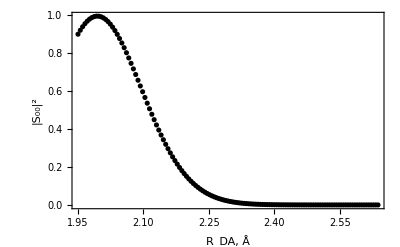

```mathematica
ListPlot[
{Table[{RDA[x],SH[x,0,0]^2},{x,0,1.3,0.01}]},
PlotStyle->{Black,Red},
PlotRange->All,
Axes->False,Frame->True,
FrameLabel->{"R_DA, Å","|S_00|^2"}
]
```

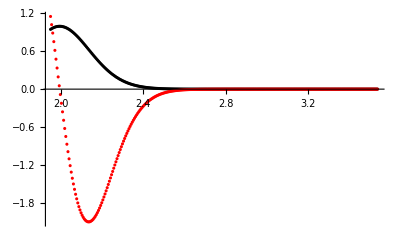

```mathematica
ListPlot[
{Table[{RDA[x],SH[x,0,0]},{x,0,3.,0.01}],
Table[{RDA[x],dSH[x,0,0]},{x,0.,3.,0.01}]},
PlotStyle->{Black,Red},
PlotRange->All
]
```

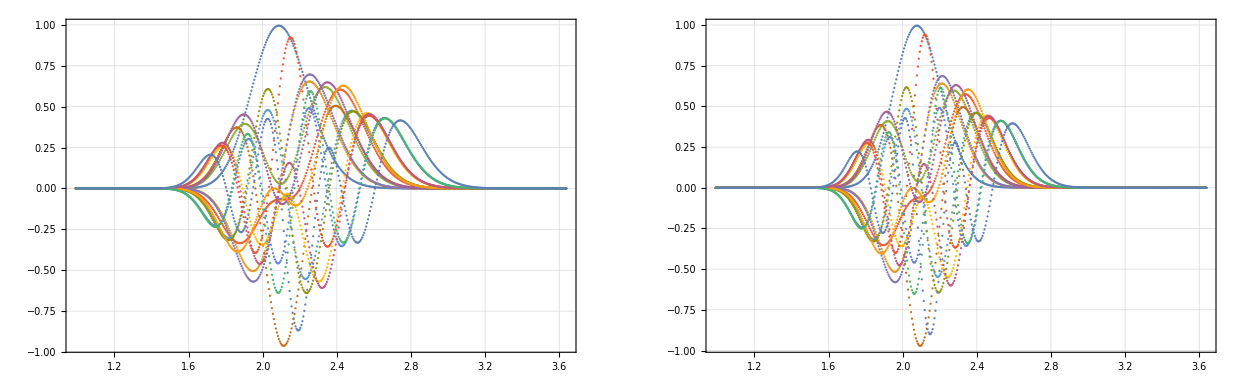

```mathematica
GraphicsRow[{
ListPlot[{
Table[{RDA[x],SH[x,0,0]},{x,-2.,3.,0.01}],
Table[{RDA[x],SH[x,0,1]},{x,-2.,3.,0.01}],
Table[{RDA[x],SH[x,0,2]},{x,-2.,3.,0.01}],
Table[{RDA[x],SH[x,0,3]},{x,-2.,3.,0.01}],
Table[{RDA[x],SH[x,1,0]},{x,-2.,3.,0.01}],
Table[{RDA[x],SH[x,1,1]},{x,-2.,3.,0.01}],
Table[{RDA[x],SH[x,1,2]},{x,-2.,3.,0.01}],
Table[{RDA[x],SH[x,1,3]},{x,-2.,3.,0.01}],
Table[{RDA[x],SH[x,2,0]},{x,-2.,3.,0.01}],
Table[{RDA[x],SH[x,2,1]},{x,-2.,3.,0.01}],
Table[{RDA[x],SH[x,2,2]},{x,-2.,3.,0.01}],
Table[{RDA[x],SH[x,2,3]},{x,-2.,3.,0.01}],
Table[{RDA[x],SH[x,3,0]},{x,-2.,3.,0.01}],
Table[{RDA[x],SH[x,3,1]},{x,-2.,3.,0.01}],
Table[{RDA[x],SH[x,3,2]},{x,-2.,3.,0.01}],
Table[{RDA[x],SH[x,3,3]},{x,-2.,3.,0.01}]
},
PlotRange->All,ImageSize->Large,PlotTheme->"Detailed"],
ListPlot[{
Table[{RDA[x],SD[x,0,0]},{x,-2.,3.,0.01}],
Table[{RDA[x],SD[x,0,1]},{x,-2.,3.,0.01}],
Table[{RDA[x],SD[x,0,2]},{x,-2.,3.,0.01}],
Table[{RDA[x],SD[x,0,3]},{x,-2.,3.,0.01}],
Table[{RDA[x],SD[x,1,0]},{x,-2.,3.,0.01}],
Table[{RDA[x],SD[x,1,1]},{x,-2.,3.,0.01}],
Table[{RDA[x],SD[x,1,2]},{x,-2.,3.,0.01}],
Table[{RDA[x],SD[x,1,3]},{x,-2.,3.,0.01}],
Table[{RDA[x],SD[x,2,0]},{x,-2.,3.,0.01}],
Table[{RDA[x],SD[x,2,1]},{x,-2.,3.,0.01}],
Table[{RDA[x],SD[x,2,2]},{x,-2.,3.,0.01}],
Table[{RDA[x],SD[x,2,3]},{x,-2.,3.,0.01}],
Table[{RDA[x],SD[x,3,0]},{x,-2.,3.,0.01}],
Table[{RDA[x],SD[x,3,1]},{x,-2.,3.,0.01}],
Table[{RDA[x],SD[x,3,2]},{x,-2.,3.,0.01}],
Table[{RDA[x],SD[x,3,3]},{x,-2.,3.,0.01}]
},
PlotRange->All,ImageSize->Large,PlotTheme->"Detailed"]
}]
```

```mathematica
sh=Interpolation[Table[{{x},SH[x,1,3]},{x,-2,3,0.01}],Method->"Spline",InterpolationOrder->3]
```

InterpolatingFunction[{{-2., 3.}}, <>]

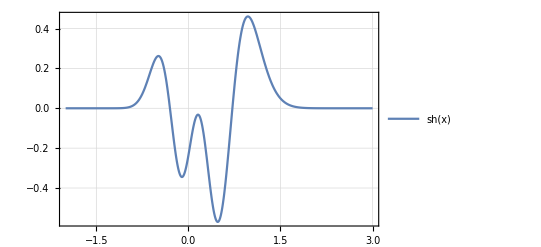

```mathematica
Plot[sh[x],{x,-2,3},PlotRange->All,PlotTheme->"Detailed"]
```

```mathematica
Table[N[αH4[R0[2.61],i,j],9],{i,0,3},{j,0,3}]//TableForm
```

9.14749835 | 7.80960917 | 6.39593806 | 4.8528198
7.78252133 | 6.14685052 | 4.2978439 | 1.94058239
6.31004264 | 4.19364992 | 1.53263722 | -3.14117891
4.67466223 | 1.58843657 | -3.55815058 | -130.270313

```mathematica
Table[N[αD4[R0[2.61],i,j],9],{i,0,3},{j,0,3}]//TableForm
```

13.2977048 | 11.9856288 | 10.6247663 | 9.19194782
11.9567599 | 10.4643268 | 8.87641918 | 7.12592649
10.5464151 | 8.81001963 | 6.90131537 | 4.65499758
9.04462189 | 6.94884408 | 4.52172253 | 1.29022871

```mathematica
Table[N[γH4[R0[2.61],i,j],9],{i,0,3},{j,0,3}]//TableForm
```

6.81720697 | 7.80314895 | 8.85364354 | 10.1531463
7.81155338 | 9.79744392 | 12.5812144 | 18.2107289
9.00195163 | 12.9710094 | 20.3144151 | 48.7263585
10.6003142 | 20.106639 | 52.8929998 | 17044.0709

```mathematica
Table[N[γD4[R0[2.61],i,j],9],{i,0,3},{j,0,3}]//TableForm
```

9.63664537 | 10.5865011 | 11.5668798 | 12.6540586
10.5859799 | 12.1160701 | 13.9000211 | 16.2895038
11.6509657 | 14.0644562 | 17.1970455 | 22.2195137
12.9112425 | 16.8608726 | 22.7895628 | 35.4758353

### Quality of expansions for harmonic overlaps:

```mathematica
SHexp1[R_,Req_,i_,j_]:=SH[R0[Req],i,j]Exp[-αH4[R0[Req],i,j](R0[R]-R0[Req])];
SHexp2[R_,Req_,i_,j_]:=SH[R0[Req],i,j]Exp[-αH4[R0[Req],i,j](R0[R]-R0[Req])-1/2 γH4[R0[Req],i,j](R0[R]-R0[Req])^2];
```

```mathematica
SDexp1[R_,Req_,i_,j_]:=SD[R0[Req],i,j]Exp[-αD4[R0[Req],i,j](R0[R]-R0[Req])];
SDexp2[R_,Req_,i_,j_]:=SD[R0[Req],i,j]Exp[-αD4[R0[Req],i,j](R0[R]-R0[Req])-1/2 γD4[R0[Req],i,j](R0[R]-R0[Req])^2];
```

NIntegrate::ncvs: NIntegrate failed to converge near the apparently non-integrable singularity at x$151194 = ∞.

General::stop: Further output of NIntegrate::ncvs will be suppressed during this calculation.

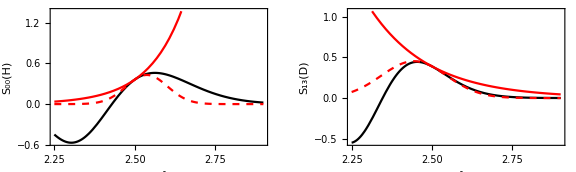

```mathematica
RR=2.5;
GraphicsRow[
{
Plot[{SH[R0[R],1,3],SHexp1[R,RR,1,3],SHexp2[R,RR,1,3]},{R,2.25,2.9},
PlotStyle->{Black,Red,{Red,Dashed}},
Axes->False,Frame->True,
FrameLabel->{"R_0(Å)","S_00(H)"}],
Plot[{SD[R0[R],1,3],SDexp1[R,RR,1,3],SDexp2[R,RR,1,3]},{R,2.25,2.9},
PlotStyle->{Black,Red,{Red,Dashed}},
PlotStyle->{Black,Red,{Red,Dashed}},
Axes->False,Frame->True,
FrameLabel->{"R_0(Å)","S_13(D)"}]
},
ImageSize->Large]
```

NIntegrate::ncvs: NIntegrate failed to converge near the apparently non-integrable singularity at x$256867 = ∞.

General::stop: Further output of NIntegrate::ncvs will be suppressed during this calculation.

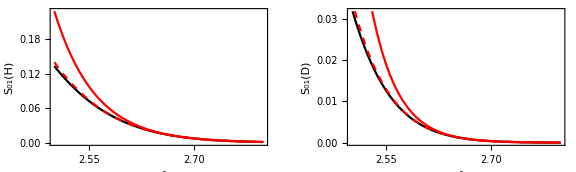

```mathematica
RR=2.7;
GraphicsRow[
{
Plot[{SH[R0[R],0,1],SHexp1[R,RR,0,1],SHexp2[R,RR,0,1]},{R,2.5,2.8},
PlotStyle->{Black,Red,{Red,Dashed}},
Axes->False,Frame->True,
FrameLabel->{"R_0(Å)","S_01(H)"}],
Plot[{SD[R0[R],0,1],SDexp1[R,RR,0,1],SDexp2[R,RR,0,1]},{R,2.5,2.8},
PlotStyle->{Black,Red,{Red,Dashed}},
Axes->False,Frame->True,
FrameLabel->{"R_0(Å)","S_01(D)"}]
},
ImageSize->Large]
```

NIntegrate::ncvs: NIntegrate failed to converge near the apparently non-integrable singularity at x$277657 = ∞.

General::stop: Further output of NIntegrate::ncvs will be suppressed during this calculation.

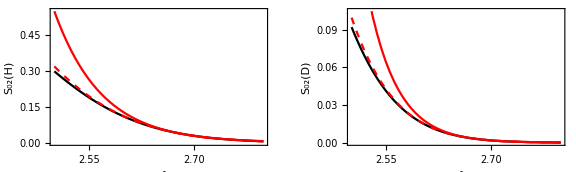

```mathematica
RR=2.7;
GraphicsRow[
{
Plot[{SH[R0[R],0,2],SHexp1[R,RR,0,2],SHexp2[R,RR,0,2]},{R,2.5,2.8},
PlotStyle->{Black,Red,{Red,Dashed}},
Axes->False,Frame->True,
FrameLabel->{"R_0(Å)","S_02(H)"}],
Plot[{SD[R0[R],0,2],SDexp1[R,RR,0,2],SDexp2[R,RR,0,2]},{R,2.5,2.8},
PlotStyle->{Black,Red,{Red,Dashed}},
Axes->False,Frame->True,
FrameLabel->{"R_0(Å)","S_02(D)"}]
},
ImageSize->Large]
```

### Spline all the distance dependencies

```mathematica
Clear[SHs,SHtable,SDs,SDtable]
```

```mathematica
Nbound=5;
```

```mathematica
Array[SHs,{Nbound+1,Nbound+1},{0,0}];
Array[SHtable,{Nbound+1,Nbound+1},{0,0}];
```

```mathematica
Monitor[Do[SHtable[i,j]=ParallelTable[{Ri,SH[Ri,i,j]},{Ri,-3.0,4.0,0.01}],{i,0,Nbound},{j,0,Nbound}],{i,j}]
```

```mathematica
Do[SHs[i,j]=Interpolation[SHtable[i,j],Method->"Spline",InterpolationOrder->3],{i,0,Nbound},{j,0,Nbound}]
```

```mathematica
Array[SDs,{Nbound+1,Nbound+1},{0,0}];
Array[SDtable,{Nbound+1,Nbound+1},{0,0}];
```

```mathematica
Monitor[Do[SDtable[i,j]=ParallelTable[{Ri,SD[Ri,i,j]},{Ri,-3.0,4.0,0.01}],{i,0,Nbound},{j,0,Nbound}],{i,j}]
```

```mathematica
Do[SDs[i,j]=Interpolation[SDtable[i,j],Method->"Spline",InterpolationOrder->3],{i,0,Nbound},{j,0,Nbound}];
```

## Comparison against Pengfei’s calculations

Read Pengfei’s overlap integrals data

```mathematica
PdataH=ReadList["Hydrogen_R_Suv.txt",{Real,Number,Number,Real }];
PdataD=ReadList["Deuterium_R_Suv.txt",{Real,Number,Number,Real }];
```

```mathematica
Clear[PSHlist,PSDlist]
```

```mathematica
Array[PSHlist,{6,6},{0,0}];
Array[PSDlist,{6,6},{0,0}];
```

```mathematica
Do[
PSHlist[i,j]={};
PSDlist[i,j]={},
{i,0,5},{j,0,5}];
```

```mathematica
Do[
AppendTo[PSHlist[PdataH⟦i⟧⟦2⟧,PdataH⟦i⟧⟦3⟧],{PdataH⟦i⟧⟦1⟧,PdataH⟦i⟧⟦4⟧}];
AppendTo[PSDlist[PdataD⟦i⟧⟦2⟧,PdataD⟦i⟧⟦3⟧],{PdataD⟦i⟧⟦1⟧,PdataD⟦i⟧⟦4⟧}],
{i,Length[PdataH]}];
```

```mathematica
SHs[0,0]
```

InterpolatingFunction[{{-3., 4.}}, <>]

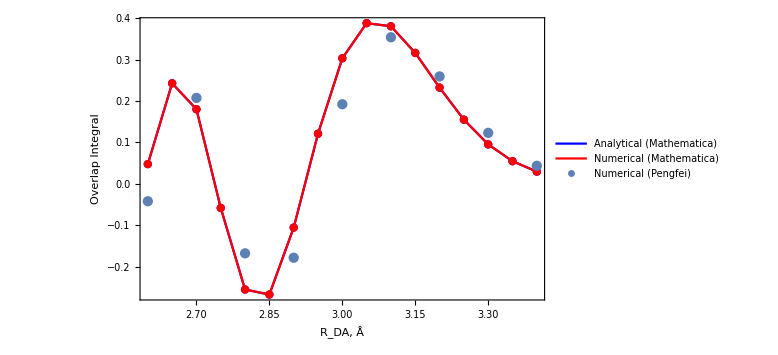

```mathematica
μ=5;
ν=5;
Show[
ListLinePlot[Table[{R,FCH[R0[R],μ,ν]},{R,2.6,3.4,0.05}],PlotRange->All,PlotStyle->Blue,Mesh->All,Axes->False,Frame->True,ImageSize->Large,FrameLabel->{"R_DA, Å","Overlap Integral"},BaseStyle->{FontSize->16},PlotLegends->{"Analytical (Mathematica)"}],
ListLinePlot[Table[{R,SH[R0[R],μ,ν]},{R,2.6,3.4,0.05}],PlotRange->All,PlotStyle->Red,Mesh->All,Axes->False,Frame->True,ImageSize->Large,FrameLabel->{"R_DA, Å","Overlap Integral"},BaseStyle->{FontSize->16},PlotLegends->{"Numerical (Mathematica)"}],
ListPlot[PSHlist[μ,ν],PlotRange->All,PlotLegends->{"Numerical (Pengfei)"}]
]
```

## Averaging of overlap integral (a la Ulstrup-Kuznetsov)

Quantum and classical distribution functions for harmonic R-oscillator:

```mathematica
PQ[T_,R_,μ_,ω_,x_]:=SetAccuracy[√((μ Dalton ω cm2au)/(π ℏ^2)Tanh[(ω cm2au)/(2kb T)])Exp[-(μ Dalton ω cm2au)/ℏ^2 Tanh[(ω cm2au)/(2kb T)](x-R)^2],AccN];
```

```mathematica
PC[T_,R_,μ_,ω_,x_]:=SetAccuracy[√((μ Dalton (ω cm2au)^2)/(2π kb T))Exp[-1/(2kb T)μ Dalton (ω cm2au)^2(x-R)^2],AccN];
```

Classical pair distribution function for the donor-acceptor distance (g(R)=e^(-β w(R))):

```mathematica
PG[T_,A_,B_,x_]:=SetAccuracy[Exp[-(kcal2au A Exp[-B x])/(kb T)],AccN];
```

Averaged (actual) Franck-Condon factors:

```mathematica
n=10;{absc,weights,errweights}=NIntegrate`GaussKronrodRuleData[n,AccN];
```

```mathematica
FWH[T_,R_,μ_,ω_,i_,j_,fun_]:=Module[{a,b,integrand,integral,error,regions,tol,r1,r2,c,x},
integrand[x_]:=Abs[SHs[i,j][x]]^2 fun[T,R,μ,ω,x];
a=0;b=3;
tol=10^-6;
{integral,error}=(b-a)Total@MapThread[{integrand[#1]#2,integrand[#1]#3}&,{Rescale[absc,{0,1},{a,b}],weights,errweights}];
regions={{{a,b},integral,Abs[error]}};
While[Abs[error]>= Abs[tol*integral],
(* splitting of the region with the largest error *)
{a,b}=regions⟦1,1⟧;c=(a+b)/2;

(* integration of the left region *)
{integral,error}=(c-a)Total@MapThread[{integrand[#1]#2,integrand[#1]#3}&,{Rescale[absc,{0,1},{a,c}],weights,errweights}];
r1={{a,c},integral,Abs[error]};

(* integration of the right region *)
{integral,error}=(b-c)Total@MapThread[{integrand[#1]#2,integrand[#1]#3}&,{Rescale[absc,{0,1},{c,b}],weights,errweights}];
r2={{c,b},integral,Abs[error]};

(* sort the regions: the largest error one is the first *)
regions=Join[{r1,r2},Rest[regions]];
regions=Sort[regions,#1⟦3⟧>#2⟦3⟧&];

(* global integral and error *)
{integral,error}=Total[Map[Rest[#1]&,regions]];

];
integral];
```

```mathematica
FWD[T_,R_,μ_,ω_,i_,j_,fun_]:=Module[{a,b,integrand,integral,error,regions,tol,r1,r2,c,x},
integrand[x_]:=Abs[SDs[i,j][x]]^2 fun[T,R,μ,ω,x];
a=0;b=3;
tol=10^-6;
{integral,error}=(b-a)Total@MapThread[{integrand[#1]#2,integrand[#1]#3}&,{Rescale[absc,{0,1},{a,b}],weights,errweights}];
regions={{{a,b},integral,Abs[error]}};
While[Abs[error]>= Abs[tol*integral],
(* splitting of the region with the largest error *)
{a,b}=regions⟦1,1⟧;c=(a+b)/2;
(* integration of the left region *)
{integral,error}=(c-a)Total@MapThread[{integrand[#1]#2,integrand[#1]#3}&,{Rescale[absc,{0,1},{a,c}],weights,errweights}];
r1={{a,c},integral,Abs[error]};
(* integration of the right region *)
{integral,error}=(b-c)Total@MapThread[{integrand[#1]#2,integrand[#1]#3}&,{Rescale[absc,{0,1},{c,b}],weights,errweights}];
r2={{c,b},integral,Abs[error]};
(* sort the regions: the largest error one is the first *)
regions=Join[{r1,r2},Rest[regions]];
regions=Sort[regions,#1⟦3⟧>#2⟦3⟧&];
(* global integral and error *)
{integral,error}=Total[Map[Rest[#1]&,regions]];
];
integral];
```

Franck-Condon factors averaged with the pair distribution function for repulsive potential of mean force:

```mathematica
FWGH[T_,A_,B_,i_,j_]:=Module[{a,b,integrand,integral,error,regions,tol,r1,r2,c,x},
integrand[x_]:=Abs[SHs[i,j][x]]^2 PG[T,A,B,RDA[x]];
a=0;b=3;
tol=10^-6;
{integral,error}=(b-a)Total@MapThread[{integrand[#1]#2,integrand[#1]#3}&,{Rescale[absc,{0,1},{a,b}],weights,errweights}];
regions={{{a,b},integral,Abs[error]}};
While[Abs[error]>= Abs[tol*integral],
(* splitting of the region with the largest error *)
{a,b}=regions⟦1,1⟧;c=(a+b)/2;

(* integration of the left region *)
{integral,error}=(c-a)Total@MapThread[{integrand[#1]#2,integrand[#1]#3}&,{Rescale[absc,{0,1},{a,c}],weights,errweights}];
r1={{a,c},integral,Abs[error]};

(* integration of the right region *)
{integral,error}=(b-c)Total@MapThread[{integrand[#1]#2,integrand[#1]#3}&,{Rescale[absc,{0,1},{c,b}],weights,errweights}];
r2={{c,b},integral,Abs[error]};

(* sort the regions: the largest error one is the first *)
regions=Join[{r1,r2},Rest[regions]];
regions=Sort[regions,#1⟦3⟧>#2⟦3⟧&];

(* global integral and error *)
{integral,error}=Total[Map[Rest[#1]&,regions]];

];
integral];
FWGD[T_,A_,B_,i_,j_]:=Module[{a,b,integrand,integral,error,regions,tol,r1,r2,c,x},
integrand[x_]:=Abs[SDs[i,j][x]]^2 PG[T,A,B,RDA[x]];
a=0;b=3;
tol=10^-6;
{integral,error}=(b-a)Total@MapThread[{integrand[#1]#2,integrand[#1]#3}&,{Rescale[absc,{0,1},{a,b}],weights,errweights}];
regions={{{a,b},integral,Abs[error]}};
While[Abs[error]>= Abs[tol*integral],
(* splitting of the region with the largest error *)
{a,b}=regions⟦1,1⟧;c=(a+b)/2;

(* integration of the left region *)
{integral,error}=(c-a)Total@MapThread[{integrand[#1]#2,integrand[#1]#3}&,{Rescale[absc,{0,1},{a,c}],weights,errweights}];
r1={{a,c},integral,Abs[error]};

(* integration of the right region *)
{integral,error}=(b-c)Total@MapThread[{integrand[#1]#2,integrand[#1]#3}&,{Rescale[absc,{0,1},{c,b}],weights,errweights}];
r2={{c,b},integral,Abs[error]};

(* sort the regions: the largest error one is the first *)
regions=Join[{r1,r2},Rest[regions]];
regions=Sort[regions,#1⟦3⟧>#2⟦3⟧&];

(* global integral and error *)
{integral,error}=Total[Map[Rest[#1]&,regions]];

];
integral];
```

Averaged (quadratic expansion) Franck-Condon factors:

```mathematica
LFWH[T_,R_,μ_,ω_,i_,j_,fun_]:=Module[{x0,a,b,integrand,integral,error,regions,tol,r1,r2,c,x},
x0=R;
integrand[x_]:=Abs[SHs[i,j][x0]]^2 Exp[-2αH[x0,i,j](x-x0)]fun[T,R,μ,ω,x];
a=0;b=3;
tol=10^-6;
{integral,error}=(b-a)Total@MapThread[{integrand[#1]#2,integrand[#1]#3}&,{Rescale[absc,{0,1},{a,b}],weights,errweights}];
regions={{{a,b},integral,Abs[error]}};
While[Abs[error]>= Abs[tol*integral],
(* splitting of the region with the largest error *)
{a,b}=regions⟦1,1⟧;c=(a+b)/2;

(* integration of the left region *)
{integral,error}=(c-a)Total@MapThread[{integrand[#1]#2,integrand[#1]#3}&,{Rescale[absc,{0,1},{a,c}],weights,errweights}];
r1={{a,c},integral,Abs[error]};

(* integration of the right region *)
{integral,error}=(b-c)Total@MapThread[{integrand[#1]#2,integrand[#1]#3}&,{Rescale[absc,{0,1},{c,b}],weights,errweights}];
r2={{c,b},integral,Abs[error]};

(* sort the regions: the largest error one is the first *)
regions=Join[{r1,r2},Rest[regions]];
regions=Sort[regions,#1⟦3⟧>#2⟦3⟧&];

(* global integral and error *)
{integral,error}=Total[Map[Rest[#1]&,regions]];

];
integral];
QFWH[T_,R_,μ_,ω_,i_,j_,fun_]:=Module[{x0,a,b,integrand,integral,error,regions,tol,r1,r2,c,x},
x0=R;
integrand[x_]:=Abs[SHs[i,j][x0]]^2 Exp[-2αH[x0,i,j](x-x0)-γH[x0,i,j](x-x0)^2]fun[T,R,μ,ω,x];
a=0;b=3;
tol=10^-6;
{integral,error}=(b-a)Total@MapThread[{integrand[#1]#2,integrand[#1]#3}&,{Rescale[absc,{0,1},{a,b}],weights,errweights}];
regions={{{a,b},integral,Abs[error]}};
While[Abs[error]>= Abs[tol*integral],
(* splitting of the region with the largest error *)
{a,b}=regions⟦1,1⟧;c=(a+b)/2;

(* integration of the left region *)
{integral,error}=(c-a)Total@MapThread[{integrand[#1]#2,integrand[#1]#3}&,{Rescale[absc,{0,1},{a,c}],weights,errweights}];
r1={{a,c},integral,Abs[error]};

(* integration of the right region *)
{integral,error}=(b-c)Total@MapThread[{integrand[#1]#2,integrand[#1]#3}&,{Rescale[absc,{0,1},{c,b}],weights,errweights}];
r2={{c,b},integral,Abs[error]};

(* sort the regions: the largest error one is the first *)
regions=Join[{r1,r2},Rest[regions]];
regions=Sort[regions,#1⟦3⟧>#2⟦3⟧&];

(* global integral and error *)
{integral,error}=Total[Map[Rest[#1]&,regions]];

];
integral];
```

```mathematica
LFWD[T_,R_,μ_,ω_,i_,j_,fun_]:=Module[{x0,a,b,integrand,integral,error,regions,tol,r1,r2,c,x},
x0=R;
integrand[x_]:=Abs[SDs[i,j][x0]]^2 Exp[-2αD[x0,i,j](x-x0)]fun[T,R,μ,ω,x];
a=0;b=3;
tol=10^-6;
{integral,error}=(b-a)Total@MapThread[{integrand[#1]#2,integrand[#1]#3}&,{Rescale[absc,{0,1},{a,b}],weights,errweights}];
regions={{{a,b},integral,Abs[error]}};
While[Abs[error]>= Abs[tol*integral],
(* splitting of the region with the largest error *)
{a,b}=regions⟦1,1⟧;c=(a+b)/2;

(* integration of the left region *)
{integral,error}=(c-a)Total@MapThread[{integrand[#1]#2,integrand[#1]#3}&,{Rescale[absc,{0,1},{a,c}],weights,errweights}];
r1={{a,c},integral,Abs[error]};

(* integration of the right region *)
{integral,error}=(b-c)Total@MapThread[{integrand[#1]#2,integrand[#1]#3}&,{Rescale[absc,{0,1},{c,b}],weights,errweights}];
r2={{c,b},integral,Abs[error]};

(* sort the regions: the largest error one is the first *)
regions=Join[{r1,r2},Rest[regions]];
regions=Sort[regions,#1⟦3⟧>#2⟦3⟧&];

(* global integral and error *)
{integral,error}=Total[Map[Rest[#1]&,regions]];

];
integral];
QFWD[T_,R_,μ_,ω_,i_,j_,fun_]:=Module[{x0,a,b,integrand,integral,error,regions,tol,r1,r2,c,x},
x0=R;
integrand[x_]:=Abs[SDs[i,j][x0]]^2 Exp[-2αD[x0,i,j](x-x0)-γD[x0,i,j](x-x0)^2]fun[T,R,μ,ω,x];
a=0;b=3;
tol=10^-6;
{integral,error}=(b-a)Total@MapThread[{integrand[#1]#2,integrand[#1]#3}&,{Rescale[absc,{0,1},{a,b}],weights,errweights}];
regions={{{a,b},integral,Abs[error]}};
While[Abs[error]>= Abs[tol*integral],
(* splitting of the region with the largest error *)
{a,b}=regions⟦1,1⟧;c=(a+b)/2;

(* integration of the left region *)
{integral,error}=(c-a)Total@MapThread[{integrand[#1]#2,integrand[#1]#3}&,{Rescale[absc,{0,1},{a,c}],weights,errweights}];
r1={{a,c},integral,Abs[error]};

(* integration of the right region *)
{integral,error}=(b-c)Total@MapThread[{integrand[#1]#2,integrand[#1]#3}&,{Rescale[absc,{0,1},{c,b}],weights,errweights}];
r2={{c,b},integral,Abs[error]};

(* sort the regions: the largest error one is the first *)
regions=Join[{r1,r2},Rest[regions]];
regions=Sort[regions,#1⟦3⟧>#2⟦3⟧&];

(* global integral and error *)
{integral,error}=Total[Map[Rest[#1]&,regions]];

];
integral];
```

### Rates:

```mathematica
RateUKqH[T_,Δ_,λ_,R_,μ_,ω_,i_,j_]:=Module[{A0,A1,A2,dG,Λ,Ea},
dG=Δ*kcal2au;
Λ=λ*kcal2au;
A0=prefactor*V^2;
A1=FWH[T,R,μ,ω,i,j,PQ];
A2=√(π/(kb T Λ));
Ea=(dG+Λ+E2[j]-E2[0]-E1[i]+E1[0])^2/(4Λ);
A0*A1*A2*Exp[-Ea/(kb T)]];
```

```mathematica
RateQUKqH[T_,Δ_,λ_,R_,μ_,ω_,i_,j_]:=Module[{A0,A1,A2,dG,Λ,Ea},
dG=Δ*kcal2au;
Λ=λ*kcal2au;
A0=prefactor*V^2;
A1=QFWH[T,R,μ,ω,i,j,PQ];
A2=√(π/(kb T Λ));
Ea=(dG+Λ+E2[j]-E2[0]-E1[i]+E1[0])^2/(4Λ);
A0*A1*A2*Exp[-Ea/(kb T)]];
RateLUKqH[T_,Δ_,λ_,R_,μ_,ω_,i_,j_]:=Module[{A0,A1,A2,dG,Λ,Ea},
dG=Δ*kcal2au;
Λ=λ*kcal2au;
A0=prefactor*V^2;
A1=LFWH[T,R,μ,ω,i,j,PQ];
A2=√(π/(kb T Λ));
Ea=(dG+Λ+E2[j]-E2[0]-E1[i]+E1[0])^2/(4Λ);
A0*A1*A2*Exp[-Ea/(kb T)]];
```

```mathematica
RateUKqD[T_,Δ_,λ_,R_,μ_,ω_,i_,j_]:=Module[{A0,A1,A2,dG,Λ,Ea},
dG=Δ*kcal2au;
Λ=λ*kcal2au;
A0=prefactor*V^2;
A1=FWD[T,R,μ,ω,i,j,PQ];
A2=√(π/(kb T Λ));
Ea=(dG+Λ+E2D[j]-E2D[0]-E1D[i]+E1D[0])^2/(4Λ);
A0*A1*A2*Exp[-Ea/(kb T)]];
```

```mathematica
RateQUKqD[T_,Δ_,λ_,R_,μ_,ω_,i_,j_]:=Module[{A0,A1,A2,dG,Λ,Ea},
dG=Δ*kcal2au;
Λ=λ*kcal2au;
A0=prefactor*V^2;
A1=QFWD[T,R,μ,ω,i,j,PQ];
A2=√(π/(kb T Λ));
Ea=(dG+Λ+E2D[j]-E2D[0]-E1D[i]+E1D[0])^2/(4Λ);
A0*A1*A2*Exp[-Ea/(kb T)]];
RateLUKqD[T_,Δ_,λ_,R_,μ_,ω_,i_,j_]:=Module[{A0,A1,A2,dG,Λ,Ea},
dG=Δ*kcal2au;
Λ=λ*kcal2au;
A0=prefactor*V^2;
A1=QFWD[T,R,μ,ω,i,j,PQ];
A2=√(π/(kb T Λ));
Ea=(dG+Λ+E2D[j]-E2D[0]-E1D[i]+E1D[0])^2/(4Λ);
A0*A1*A2*Exp[-Ea/(kb T)]];
```

```mathematica
TotalrateUKqH[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j},Sum[PCH[T,i,n]Sum[RateUKqH[T,Δ,λ,R,μ,ω,i,j],{j,0,m}],{i,0,n}]];
```

```mathematica
TotalrateQUKqH[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j},Sum[PCH[T,i,n]Sum[RateQUKqH[T,Δ,λ,R,μ,ω,i,j],{j,0,m}],{i,0,n}]];
TotalrateLUKqH[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j},Sum[PCH[T,i,n]Sum[RateLUKqH[T,Δ,λ,R,μ,ω,i,j],{j,0,m}],{i,0,n}]];
```

```mathematica
TotalrateUKqD[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j},Sum[PCD[T,i,n]Sum[RateUKqD[T,Δ,λ,R,μ,ω,i,j],{j,0,m}],{i,0,n}]];
```

```mathematica
TotalrateQUKqD[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j},Sum[PCD[T,i,n]Sum[RateQUKqD[T,Δ,λ,R,μ,ω,i,j],{j,0,m}],{i,0,n}]];
TotalrateLUKqD[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j},Sum[PCD[T,i,n]Sum[RateLUKqD[T,Δ,λ,R,μ,ω,i,j],{j,0,m}],{i,0,n}]];
```

```mathematica
KIEUKq=Function[{T,Δ,λ,R,μ,ω,n,m},TotalrateUKqH[T,Δ,λ,R,μ,ω,n,m]/TotalrateUKqD[T,Δ,λ,R,μ,ω,n,m]];
```

```mathematica
KIEQUKq=Function[{T,Δ,λ,R,μ,ω,n,m},TotalrateQUKqH[T,Δ,λ,R,μ,ω,n,m]/TotalrateQUKqD[T,Δ,λ,R,μ,ω,n,m]];
KIELUKq=Function[{T,Δ,λ,R,μ,ω,n,m},TotalrateQUKqH[T,Δ,λ,R,μ,ω,n,m]/TotalrateQUKqD[T,Δ,λ,R,μ,ω,n,m]];
```

```mathematica
RateUKH[T_,Δ_,λ_,R_,μ_,ω_,i_,j_]:=Module[{A0,A1,A2,dG,Λ,Ea},
dG=Δ*kcal2au;
Λ=λ*kcal2au;
A0=prefactor*V^2;
A1=FWH[T,R,μ,ω,i,j,PC];
A2=√(π/(kb T Λ));
Ea=(dG+Λ+E2[j]-E2[0]-E1[i]+E1[0])^2/(4Λ);
A0*A1*A2*Exp[-Ea/(kb T)]];
```

```mathematica
RateUKGH[T_,Δ_,λ_,A_,B_,i_,j_]:=Module[{A0,A1,A2,dG,Λ,Ea},
dG=Δ*kcal2au;
Λ=λ*kcal2au;
A0=prefactor*V^2;
A1=FWGH[T,A,B,i,j];
A2=√(π/(kb T Λ));
Ea=(dG+Λ+E2[j]-E2[0]-E1[i]+E1[0])^2/(4Λ);
A0*A1*A2*Exp[-Ea/(kb T)]];
```

```mathematica
RateQUKH[T_,Δ_,λ_,R_,μ_,ω_,i_,j_]:=Module[{A0,A1,A2,dG,Λ,Ea},
dG=Δ*kcal2au;
Λ=λ*kcal2au;
A0=prefactor*V^2;
A1=QFWH[T,R,μ,ω,i,j,PC];
A2=√(π/(kb T Λ));
Ea=(dG+Λ+E2[j]-E2[0]-E1[i]+E1[0])^2/(4Λ);
A0*A1*A2*Exp[-Ea/(kb T)]];
RateLUKH[T_,Δ_,λ_,R_,μ_,ω_,i_,j_]:=Module[{A0,A1,A2,dG,Λ,Ea},
dG=Δ*kcal2au;
Λ=λ*kcal2au;
A0=prefactor*V^2;
A1=LFWH[T,R,μ,ω,i,j,PC];
A2=√(π/(kb T Λ));
Ea=(dG+Λ+E2[j]-E2[0]-E1[i]+E1[0])^2/(4Λ);
A0*A1*A2*Exp[-Ea/(kb T)]];
```

```mathematica
RateUKD[T_,Δ_,λ_,R_,μ_,ω_,i_,j_]:=Module[{A0,A1,A2,dG,Λ,Ea},
dG=Δ*kcal2au;
Λ=λ*kcal2au;
A0=prefactor*V^2;
A1=FWD[T,R,μ,ω,i,j,PC];
A2=√(π/(kb T Λ));
Ea=(dG+Λ+E2D[j]-E2D[0]-E1D[i]+E1D[0])^2/(4Λ);
A0*A1*A2*Exp[-Ea/(kb T)]];
```

```mathematica
RateUKGD[T_,Δ_,λ_,A_,B_,i_,j_]:=Module[{A0,A1,A2,dG,Λ,Ea},
dG=Δ*kcal2au;
Λ=λ*kcal2au;
A0=prefactor*V^2;
A1=FWGD[T,A,B,i,j];
A2=√(π/(kb T Λ));
Ea=(dG+Λ+E2D[j]-E2D[0]-E1D[i]+E1D[0])^2/(4Λ);
A0*A1*A2*Exp[-Ea/(kb T)]];
```

```mathematica
RateQUKD[T_,Δ_,λ_,R_,μ_,ω_,i_,j_]:=Module[{A0,A1,A2,dG,Λ,Ea},
dG=Δ*kcal2au;
Λ=λ*kcal2au;
A0=prefactor*V^2;
A1=QFWD[T,R,μ,ω,i,j,PC];
A2=√(π/(kb T Λ));
Ea=(dG+Λ+E2D[j]-E2D[0]-E1D[i]+E1D[0])^2/(4Λ);
A0*A1*A2*Exp[-Ea/(kb T)]];
RateLUKD[T_,Δ_,λ_,R_,μ_,ω_,i_,j_]:=Module[{A0,A1,A2,dG,Λ,Ea},
dG=Δ*kcal2au;
Λ=λ*kcal2au;
A0=prefactor*V^2;
A1=LFWD[T,R,μ,ω,i,j,PC];
A2=√(π/(kb T Λ));
Ea=(dG+Λ+E2D[j]-E2D[0]-E1D[i]+E1D[0])^2/(4Λ);
A0*A1*A2*Exp[-Ea/(kb T)]];
```

```mathematica
TotalrateUKH[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j},Sum[PCH[T,i,n]Sum[RateUKH[T,Δ,λ,R,μ,ω,i,j],{j,0,m}],{i,0,n}]];
TotalrateUKGH[T_,Δ_,λ_,A_,B_,n_,m_]:=Module[{i,j},Sum[PCH[T,i,n]Sum[RateUKGH[T,Δ,λ,A,B,i,j],{j,0,m}],{i,0,n}]];
TotalrateQUKH[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j},Sum[PCH[T,i,n]Sum[RateQUKH[T,Δ,λ,R,μ,ω,i,j],{j,0,m}],{i,0,n}]];
TotalrateLUKH[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j},Sum[PCH[T,i,n]Sum[RateLUKH[T,Δ,λ,R,μ,ω,i,j],{j,0,m}],{i,0,n}]];
```

```mathematica
TotalrateUKD[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j},Sum[PCD[T,i,n]Sum[RateUKD[T,Δ,λ,R,μ,ω,i,j],{j,0,m}],{i,0,n}]];
TotalrateUKGD[T_,Δ_,λ_,A_,B_,n_,m_]:=Module[{i,j},Sum[PCD[T,i,n]Sum[RateUKGD[T,Δ,λ,A,B,i,j],{j,0,m}],{i,0,n}]];
TotalrateQUKD[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j},Sum[PCD[T,i,n]Sum[RateQUKD[T,Δ,λ,R,μ,ω,i,j],{j,0,m}],{i,0,n}]];
TotalrateLUKD[T_,Δ_,λ_,R_,μ_,ω_,n_,m_]:=Module[{i,j},Sum[PCD[T,i,n]Sum[RateLUKD[T,Δ,λ,R,μ,ω,i,j],{j,0,m}],{i,0,n}]];
```

```mathematica
KIEUK=Function[{T,Δ,λ,R,μ,ω,n,m},TotalrateUKH[T,Δ,λ,R,μ,ω,n,m]/TotalrateUKD[T,Δ,λ,R,μ,ω,n,m]];
KIEUKG=Function[{T,Δ,λ,A,B,n,m},TotalrateUKGH[T,Δ,λ,A,B,n,m]/TotalrateUKGD[T,Δ,λ,A,B,n,m]];
KIEQUK=Function[{T,Δ,λ,R,μ,ω,n,m},TotalrateQUKH[T,Δ,λ,R,μ,ω,n,m]/TotalrateQUKD[T,Δ,λ,R,μ,ω,n,m]];
KIELUK=Function[{T,Δ,λ,R,μ,ω,n,m},TotalrateLUKH[T,Δ,λ,R,μ,ω,n,m]/TotalrateLUKD[T,Δ,λ,R,μ,ω,n,m]];
```